```mathematica
Clear["Global`*"];

(* ==========PARÁMETROS AJUSTABLES==========*)
nfinal=100;          (*Último sitio (la cadena va de 0 a nfinal)*)
tiempoMax=2000;       (*Tiempo de simulación*)

(*Prámetro adicional*)
ϵ=0.75;
(*Acoplamientos:beta en enlaces impares (0-1,2-3,...),betaprima en pares (1-2,3-4,...)*)
beta=(1-ϵ)/2;           (*Enlace débil*)
betaprima=(1+ϵ)/2;      (*Enlace fuerte*)
(* ==========CONSTRUCCIÓN DEL SISTEMA==========*)
(*Definimos los acoplamientos para cada enlace entre i e i+1*)
acoplamiento[i_]:=If[EvenQ[i],beta,betaprima];  (*i=0->beta,i=1->betaprima,i=2->beta,...*)
(*Condiciones de frontera:rebote en ambos extremos*)
A[-1][t_]=0;
A[nfinal+1][t_]=0;
(*Ecuaciones diferenciales*)
eqns=Table[I A[i]'[t]==-acoplamiento[i] A[i+1][t]-acoplamiento[i-1] A[i-1][t],{i,0,nfinal}];
(*Condición inicial:partícula en el sitio 0*)
ci=Table[A[i][0]==If[i==0,1,0],{i,0,nfinal}];
(*Variables*)
vars=Table[A[i],{i,0,nfinal}];
(* ==========RESOLUCIÓN NUMÉRICA==========*)
sol=NDSolve[{eqns,ci},vars,{t,0,tiempoMax}, MaxSteps->Infinity];
```

```mathematica
(* ==========ANIMACIÓN==========*)
Animate[ListPlot[Table[{i,Abs[A[i][t]/. sol[[1]]]^2},{i,0,nfinal}],PlotRange->{{0,nfinal},{0,1.1}},PlotStyle->{Blue,PointSize[0.015]},Filling->Axis,FillingStyle->Directive[Opacity[0.3],Blue],PlotLabel->Style[StringForm["SSH",beta,betaprima,t],14,Bold, Black],AxesLabel->{"Sitio n","Probabilidad |A_n(t)|.b2"},GridLines->Automatic,ImageSize->600],{t,0,tiempoMax,0.5},AnimationRunning->False]
```

```mathematica
If[180,Hue[0.5]]
```

If[180,Hue[0.5]]

```mathematica
Animate[Graphics[Table[{Hue[Arg[A[i][t]/. sol[[1]]]/(2 Pi)],PointSize[0.025],Point[{i,Abs[A[i][t]/. sol[[1]]]^2}]},{i,0,nfinal}],PlotRange->{{-1,nfinal+1},{0,1.1}},AspectRatio->0.7,Axes->True,AxesLabel->{"Sitio n","Probabilidad |A_n(t)|.b2"},GridLines->Automatic,PlotLabel->Style[StringForm["SSH    β = ``    β' = ``    t = ``",beta,betaprima,NumberForm[t,{4,2}]],14,Bold,Black],ImageSize->600],{t,0,tiempoMax,0.5},AnimationRunning->False]
```

```mathematica
Table[Arg[A[i][140]/. sol[[1]]] 180/Pi,{i,0,nfinal}]
```

{0.,-90.,180.,-90.,0.,-90.,0.,-90.,0.,90.,0.,90.,0.,90.,0.,90.,180.,-90.,180.,90.,180.,-90.,180.,-90.,0.,-90.,180.,-90.,0.,90.,0.,90.,180.,-90.,180.,-90.,0.,90.,0.,90.,180.,-90.,0.,90.,0.,90.,180.,-90.,180.,-90.,0.,90.,0.,90.,180.,-90.,0.,90.,0.,90.,180.,-90.,180.,-90.,0.,90.,0.,90.,180.,-90.,0.,90.,0.,90.,180.,-90.,180.,-90.,0.,90.,180.,-90.,180.,-90.,0.,90.,0.,90.,180.,-90.,0.,90.,0.,90.,180.,-90.,0.,90.,0.,90.,180.}

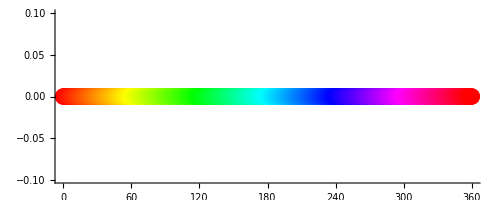

```mathematica
Graphics[Table[{Hue[x/360],PointSize[0.03],Point[{x,0}]},{x,0,360,1}],PlotRange->{{0,360},{-0.1,0.1}},Axes->True]
```

```mathematica
Table[{Arg[A[i][140]/. sol[[1]]] 180/Pi,Hue[Arg[A[i][140]/. sol[[1]]]/(2 Pi)]},{i,0,nfinal}]
```

{{0.,Hue[0.]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]},{-90.,Hue[-0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{0.,Hue[0.]},{90.,Hue[0.25]},{180.,Hue[0.5]}}

```mathematica
A[30][140] /. sol[[1]]
```

0.0326911+0. ⅈ

```mathematica
a0=Sqrt[1-(beta/betaprima)^2];
```

```mathematica
B[0]=a0;
B[1]=0;
B[i_]:=-(beta/betaprima) B[i-2];
```

```mathematica
χ[t_]:=Table[(A[i][t]/. sol[[1]])-B[i],{i,0,nfinal}];

Z[t_]:=Total[Abs[χ[t]]^2];

n[t_]:=Total[Range[0,nfinal] Abs[χ[t]]^2]/Z[t];
```

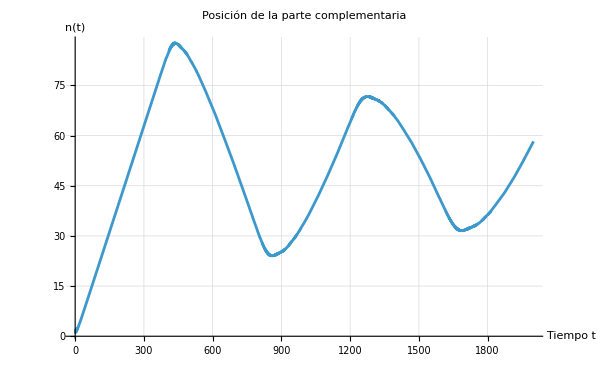

```mathematica
Plot[n[t],{t,0,tiempoMax},PlotRange->All,AxesLabel->{"Tiempo t","n(t)"},PlotLabel->"Posición de la parte complementaria",GridLines->Automatic,ImageSize->600]
```

```mathematica
dt=0.1;

v[t_]:=(n[t+dt]-n[t-dt])/(2 dt);
```

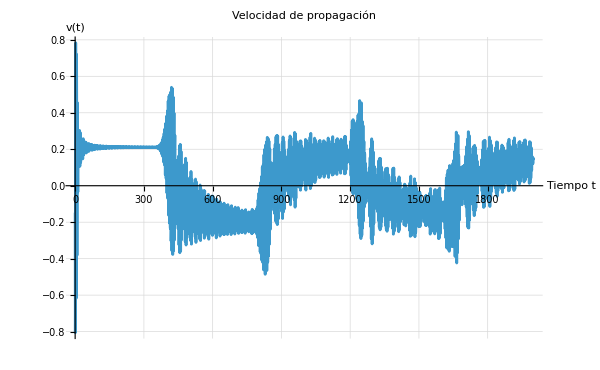

```mathematica
Plot[v[t],{t,dt,tiempoMax-dt},PlotRange->All,AxesLabel->{"Tiempo t","v(t)"},PlotLabel->"Velocidad de propagación",GridLines->Automatic,ImageSize->600]
```